Fit k(t) of both experimental and numerical data with von-Mises distribution, and fit k(t) with exponentially decay to find persistent time.
The numerical data is given by the Fokker-Planck equation:

∂/(∂t)ψ=D_R∂^2/(∂θ^2)ψ+ζ∂/(∂θ)(ψ,sinθ)

where ψ=ψ(θ,t) is the density distribution, D_R is the diffusion constant, ζ,sinθ is the light-induced external torque with ζ as the strength. Note that we have no drag coefficient in front of ∂_t ψ, namely the equation is nondimensionalized by the drag coefficient.

The von-Mises distribution is given by

ⅇ^(k,cosθ)/(2π,I_0(k))

where I_0 is the modified Bessel function of the zeroth order and k is the only fitting parameter.

This code works with the example data.

```mathematica
(*Initialize*)
ClearAll["Global`*"]
currentLocation=NotebookDirectory[];
```

```mathematica
(*Basic physics*)
FP=Subscript[D, R] D[ψ[θ,t],{θ,2}]+ζ D[ψ[θ,t]Sin[θ],θ]-D[ψ[θ,t],t];(*The Fokker-Planck equation*)
vonMises[θ_,k_]:=Exp[k Cos[θ]]/(2π BesselI[0,k])(*von-Mises distribution*)
polarVonMises[k_]:=BesselI[1, k]/BesselI[0, k](*The polarization of von-Mises distribution*)
```

```mathematica
(*Basic parameters and constants*)
(*!!!!!!!!!!!!!!!!!!!!!!!!!!!!!*)
(*These need to be set by hand*)
(*!!!!!!!!!!!!!!!!!!!!!!!!!!!!!*)
(*The following only works for the example data*)
LightTurnOn=10.;(*When the light is turned on*)
LightEnd=55.;(*When the light is turned off*)
Subscript[D, R]=0.13;(*The diffusion constant*)
timeListAddress="\\30mA\\OP_Data11\\TTD_30mAOP_Data11\\MMat_Time30mAOP_Data11.txt"(*The address of the file recording the *)
```

```mathematica
TimeList=Import[currentLocation<>"\\30mA\\OP_Data11\\TTD_30mAOP_Data11\\MMat_Time30mAOP_Data11.txt","TSV"]⟦;;,1⟧;
LightTurnOnIndex=Position[TimeList,LightTurnOn]⟦1,1⟧;
LightEndIndex=Position[TimeList,LightEnd]⟦1,1⟧;
TimeList=TimeList⟦LightTurnOnIndex;;LightEndIndex⟧-LightTurnOn;
TimeSize=Length[TimeList];
FP=Subscript[D, R] D[ψ[θ,t],{θ,2}]+ζ D[ψ[θ,t]Sin[θ],θ]-D[ψ[θ,t],t];
AddressProbDen[n_,m_]:=StringReplace[currentLocation<>"\\LightmA\\OP_DataIndex\\TTD_LightmAOP_DataIndex\\MMat_ProbDen_AvgLightmAOP_DataIndex.txt",{"Light"->ToString@LightList⟦n⟧, "Index"->ToString@IndexList⟦n,m⟧}]
ProbDen=Table[Table[Transpose[Import[AddressProbDen[n,m],"TSV"]]⟦LightTurnOnIndex;;LightEndIndex⟧,{m,1,Μ}],{n,1,Ν}];
ThetaList=Flatten@Import[currentLocation<>"\\30mA\\OP_Data11\\TTD_30mAOP_Data11\\theta.txt","TSV"];
ThetaSize=Length[ThetaList];
ThetaDiff=ThetaList⟦2⟧-ThetaList⟦1⟧;
AnaSteady[θ_,γ_]:=Exp[γ/Subscript[D, R]Cos[θ]]/(2π BesselI[0,γ/Subscript[D, R]])
PolarSteady[γ_]:=BesselI[1, γ/Subscript[D, R]]/BesselI[0, γ/Subscript[D, R]]
```

```mathematica
FitExp[n_,m_]:=(
goto=StringReplace["\\FitAll\\LightmA_DataIndex\\",{"Light"->ToString[LightList⟦n⟧], "Index"->ToString[IndexList⟦n,m⟧]}];
ProbDenSteady=Mean@ProbDen⟦n,m,-200;;⟧;
nlmExSteady=NonlinearModelFit[Table[{ThetaList⟦i⟧,ProbDenSteady⟦i⟧},{i,ThetaSize}],Exp[k Cos[θ+shift]]/(2π BesselI[0,k]),{k,shift},θ];
a=shift/.nlmExSteady["BestFitParameters"];
γ=k Subscript[D, R]/.nlmExSteady["BestFitParameters"];
Export[currentLocation<>goto<>"ExSteady.csv",{γ,a,Subscript[D, R] nlmExSteady["ParameterErrors"]⟦1⟧}];
GammaExList={};
GammaExErrorList={};
PolarExList={};
RSQExList={};
PolarExFitList={};
ThetaListShift=ThetaList+a;
MinIndex=First@Ordering@Abs[ThetaListShift-π];
ThetaListShift=Join[ThetaListShift⟦MinIndex;;⟧-2π,ThetaListShift⟦;;MinIndex-1⟧];
Do[
ProbDenShift=ProbDen⟦n,m,TimeIndex⟧;
ProbDenShift=Join[ProbDenShift⟦MinIndex;;⟧,ProbDenShift⟦;;MinIndex-1⟧];
PolarExList=Append[PolarExList,ThetaDiff Total@Table[Cos@ThetaListShift⟦i⟧ProbDenShift⟦i⟧,{i,1,ThetaSize}]];
dataEx=Table[{ThetaListShift⟦i⟧,ProbDenShift⟦i⟧},{i,1, ThetaSize}];
nlmEx=NonlinearModelFit[dataEx,Exp[k Cos[θ]]/(2π BesselI[0,k]),k,θ];
GammaEx=k Subscript[D, R]/.nlmEx["BestFitParameters"];
GammaExList=Append[GammaExList,GammaEx /γ];
GammaExErrorList=Append[GammaExErrorList,Subscript[D, R]/γ nlmEx["ParameterErrors"]⟦1⟧];
RSQExList=Append[RSQExList,nlmEx["RSquared"]];
AppendTo[PolarExFitList,PolarSteady[GammaEx]];
,{TimeIndex,TimeSize}];
GammaExFitStart=If[PolarExList⟦200⟧<0.2,400,1];
DataGammaEx=Table[{TimeList⟦i⟧,GammaExList⟦i⟧},{i,GammaExFitStart,TimeSize}];
nlmGammaEx=NonlinearModelFit[DataGammaEx,1-Exp[-(t-q)/τ],{τ,q},t];
qq=q/.nlmGammaEx["BestFitParameters"];
If[qq<0,nlmGammaEx=NonlinearModelFit[DataGammaEx,1-Exp[-t/τ],τ,t];qq=0];

PTimeExFixStart=qq;
PTimeExFixStart=Ordering[Abs[TimeList-PTimeExFixStart]]⟦1⟧;
DataPTimeEx=Table[{TimeList⟦i⟧,PolarExList⟦i⟧},{i,PTimeExFixStart,TimeSize}];
nlmPTimeEx=NonlinearModelFit[DataPTimeEx,A(1-Exp[-(t-q)/τ]),{A,τ,q},t];
qp=q/.nlmPTimeEx["BestFitParameters"];
If[qp<0,nlmPTimeEx=NonlinearModelFit[DataPTimeEx,A(1-Exp[-t/τ]),{A,τ},t];qp=0];
PTimeExFitFixStart=qp;
PTimeExFitFixStart=Ordering[Abs[TimeList-PTimeExFitFixStart]]⟦1⟧;
DataPTimeExFit=Table[{TimeList⟦i⟧,PolarExFitList⟦i⟧},{i,PTimeExFitFixStart,TimeSize}];
nlmPTimeExFit=NonlinearModelFit[DataPTimeExFit,A(1-Exp[-(t-q)/τ]),{A,τ,q},t];
qpf=q/.nlmPTimeExFit["BestFitParameters"];
If[qpf<0,nlmPTimeExFit=NonlinearModelFit[DataPTimeExFit,A(1-Exp[-t/τ]),{A,τ},t];qpf=0];
Export[currentLocation<>goto<>"FitStartTime.csv",{TimeList⟦GammaExFitStart⟧,TimeList⟦PTimeExFixStart⟧}];
Export[currentLocation<>goto<>"StartPolar.csv",qp];
Export[currentLocation<>goto<>"StartGamma.csv",qq];
Export[currentLocation<>goto<>"StartPolarFit.csv",qpf];
Export[currentLocation<>goto<>"PTimeEx.csv",τ/.nlmPTimeEx["BestFitParameters"]];
Export[currentLocation<>goto<>"PSteadyEx.csv",A/.nlmPTimeEx["BestFitParameters"]];
Export[currentLocation<>goto<>"PTimeExFit.csv",τ/.nlmPTimeExFit["BestFitParameters"]];
Export[currentLocation<>goto<>"PSteadyExFit.csv",A/.nlmPTimeExFit["BestFitParameters"]];
Export[currentLocation<>goto<>"GammaTimeEx.csv",τ/.nlmGammaEx["BestFitParameters"]];
Export[currentLocation<>goto<>"Gamma2.csv",GammaExList];
Export[currentLocation<>goto<>"PolarEx.csv",PolarExList];
Export[currentLocation<>goto<>"PolarExFit.csv",PolarExFitList];
Export[currentLocation<>goto<>"Gamma2Error.csv",GammaExErrorList];
Export[currentLocation<>goto<>"PTimeExError.csv",nlmPTimeEx["ParameterErrors"]⟦2⟧];
Export[currentLocation<>goto<>"PTimeExFitError.csv",nlmPTimeExFit["ParameterErrors"]⟦2⟧];
Export[currentLocation<>goto<>"GammaTimeExError.csv",nlmGammaEx["ParameterErrors"]⟦1⟧];
Export[currentLocation<>goto<>"FitRSQ.csv",RSQExList];
Export[currentLocation<>goto<>"RSquareEx.jpg",ListPlot[Table[{TimeList⟦i⟧,RSQExList⟦i⟧},{i,TimeSize}],PlotRange->All,PlotStyle->Blue]];
Print[{n,m}]
)
```

```mathematica
FitExp[6,5]
```

NonlinearModelFit::sszero: 搜索中的步长比由 PrecisionGoal 选项规定的容差小，但是梯度大于由 AccuracyGoal 选项指定的容差. 有可能该方法会停在一个并非局部最小值的点上.

General::stop: 在本次计算中，NonlinearModelFit::sszero 的进一步输出将被抑制.

{6,5}

```mathematica
Table[Table[FitExp[n,m],{n,Ν}],{m,Μ}]
```

{1,1}

{2,1}

{3,1}

NonlinearModelFit::sszero: 搜索中的步长比由 PrecisionGoal 选项规定的容差小，但是梯度大于由 AccuracyGoal 选项指定的容差. 有可能该方法会停在一个并非局部最小值的点上.

{4,1}

{5,1}

{6,1}

NonlinearModelFit::sszero: 搜索中的步长比由 PrecisionGoal 选项规定的容差小，但是梯度大于由 AccuracyGoal 选项指定的容差. 有可能该方法会停在一个并非局部最小值的点上.

{7,1}

NonlinearModelFit::sszero: 搜索中的步长比由 PrecisionGoal 选项规定的容差小，但是梯度大于由 AccuracyGoal 选项指定的容差. 有可能该方法会停在一个并非局部最小值的点上.

General::stop: 在本次计算中，NonlinearModelFit::sszero 的进一步输出将被抑制.

{8,1}

{9,1}

{10,1}

{1,2}

{2,2}

{3,2}

{4,2}

{5,2}

{6,2}

{7,2}

{8,2}

{9,2}

{10,2}

{1,3}

{2,3}

{3,3}

{4,3}

{5,3}

{6,3}

{7,3}

{8,3}

{9,3}

{10,3}

{1,4}

{2,4}

{3,4}

{4,4}

{5,4}

{6,4}

{7,4}

{8,4}

{9,4}

{10,4}

{1,5}

{2,5}

{3,5}

{4,5}

{5,5}

{6,5}

{7,5}

{8,5}

{9,5}

{10,5}

{1,6}

{2,6}

{3,6}

{4,6}

{5,6}

{6,6}

{7,6}

{8,6}

{9,6}

{10,6}

{1,7}

{2,7}

{3,7}

{4,7}

{5,7}

{6,7}

{7,7}

{8,7}

{9,7}

{10,7}

{1,8}

{2,8}

{3,8}

{4,8}

{5,8}

{6,8}

{7,8}

{8,8}

{9,8}

{10,8}

{1,9}

{2,9}

{3,9}

{4,9}

{5,9}

{6,9}

{7,9}

{8,9}

{9,9}

{10,9}

{1,10}

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

{2,10}

{3,10}

NonlinearModelFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，NonlinearModelFit::cvmit 的进一步输出将被抑制.

{4,10}

{5,10}

{6,10}

{7,10}

{8,10}

{9,10}

{10,10}

{{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}

```mathematica
Compare[n_,m_]:=(

goto=StringReplace["\\FitAll\\LightmA_DataIndex\\",{"Light"->ToString[LightList⟦n⟧], "Index"->ToString[IndexList⟦n,m⟧]}];
{γ,a,γError}=Flatten[Import[currentLocation<>goto<>"ExSteady.csv"]];
qq=Round[Import[currentLocation<>goto<>"StartGamma.csv","TSV"]⟦1,1⟧,0.02];
qqIndex=Quotient[qq,0.02];
ns=NDSolveValue[{FP==0/.ζ->γ,ψ[θ,0]==1/(2π),ψ[-π,t]==ψ[π,t]},ψ,{t,0,45},{θ,-π,π},MaxStepSize->0.01];
nsBig = NDSolveValue[{FP==0/.ζ->γ+γError,ψ[θ,0]==1/(2π),ψ[-π,t]==ψ[π,t]},ψ,{t,0,45},{θ,-π,π},MaxStepSize->0.01];
nsSmall = NDSolveValue[{FP==0/.ζ->γ-γError,ψ[θ,0]==1/(2π),ψ[-π,t]==ψ[π,t]},ψ,{t,0,45},{θ,-π,π},MaxStepSize->0.01];
GammaNumList={};
RSQNumList={};
PolarNumList={};
GammaExList=Flatten[Import[currentLocation<>goto<>"Gamma2.csv","TSV"]];
NumSol={};
NumSolBig={};
NumSolSmall={};
Do[
If[qqIndex+TimeIndex>TimeSize,Break[]];
GammaEx=GammaExList⟦qqIndex+TimeIndex⟧;
TimecurrentLocation=TimeList⟦TimeIndex⟧;
ProbDenShift=ProbDen⟦n,m,qqIndex+TimeIndex⟧;
(*ProbDenErrorShift=ProbDenError⟦n,m,qqIndex+TimeIndex⟧;*)
ThetaListShift=ThetaList+a;
MinIndex=First@Ordering@Abs[ThetaListShift-π];
ThetaListShift=Join[ThetaListShift⟦MinIndex;;⟧-2π,ThetaListShift⟦;;MinIndex-1⟧];
ProbDenShift=Join[ProbDenShift⟦MinIndex;;⟧,ProbDenShift⟦;;MinIndex-1⟧];
(*ProbDenErrorShift=Join[ProbDenErrorShift⟦MinIndex;;⟧,ProbDenErrorShift⟦;;MinIndex-1⟧];*)
nsList=ns[ThetaListShift,TimecurrentLocation];
nsListBig=nsBig[ThetaListShift,TimecurrentLocation];
nsListSmall=nsSmall[ThetaListShift,TimecurrentLocation];
AppendTo[PolarNumList,
{Total[Cos[ThetaListShift]nsList]ThetaDiff,
Total[Cos[ThetaListShift]nsListBig]ThetaDiff,
Total[Cos[ThetaListShift]nsListSmall]ThetaDiff}
];
dataNum=Table[{ThetaListShift⟦i⟧,nsList⟦i⟧},{i,1,ThetaSize}];
dataNumBig=Table[{ThetaListShift⟦i⟧,nsListBig⟦i⟧},{i,1,ThetaSize}];
dataNumSmall=Table[{ThetaListShift⟦i⟧,nsListSmall⟦i⟧},{i,1,ThetaSize}];
nlmNum=NonlinearModelFit[dataNum,Exp[k Cos[θ]]/(2π BesselI[0,k]),k,θ];
nlmNumBig=NonlinearModelFit[dataNumBig,Exp[k Cos[θ]]/(2π BesselI[0,k]),k,θ];
nlmNumSmall=NonlinearModelFit[dataNumSmall,Exp[k Cos[θ]]/(2π BesselI[0,k]),k,θ];
AppendTo[GammaNumList,
{k Subscript[D, R]/γ/.nlmNum["BestFitParameters"],
k Subscript[D, R]/γ/.nlmNumBig["BestFitParameters"],
k Subscript[D, R]/γ/.nlmNumSmall["BestFitParameters"]
}
];
AppendTo[RSQNumList,
{nlmNum["RSquared"],
nlmNumBig["RSquared"],
nlmNumSmall["RSquared"]
}];
AppendTo[NumSol,nsList];
AppendTo[NumSolBig,nsListBig];
AppendTo[NumSolSmall,nsListSmall];
(*MovePeak=Max[{Max@nsList,Max@ProbDenShift}]+0.1;
Export[StringReplace[currentLocation<>goto<>"Plots//Move//ComparetimeMove.jpg","time"-> ToString[Round[50TimecurrentLocation,1]]],
Show[
Plot[ns[θ,TimecurrentLocation],{θ,-π,π},PlotStyle->Red,PlotRange->{0,timePeak}],
Plot[nsSmall[θ,TimecurrentLocation],{θ,-π,π},PlotStyle->{Red,Dashed},PlotRange->{0,timePeak}],
Plot[nsBig[θ,TimecurrentLocation],{θ,-π,π},PlotStyle->{Red,Dashed},PlotRange->{0,timePeak}],
Plot[AnaSteady[θ,γ],{θ,-π,π},PlotStyle->{Black,Dotted},PlotRange->{0,timePeak}],
(*ListPlot[Table[{ThetaListShift⟦l⟧,Around[ProbDenShift⟦l⟧,ProbDenErrorShift⟦l⟧]},{l,ThetaSize}],PlotRange->{0,timePeak},*)
ListPlot[Table[{ThetaListShift⟦l⟧,ProbDenShift⟦l⟧},{l,ThetaSize}],PlotRange->{0,timePeak},PlotStyle->Blue],
Plot[AnaSteady[θ,GammaEx γ],{θ,-π,π},PlotStyle->{Blue,Dashed},PlotRange->{0,timePeak}]
]];
FixPeak=Max[ProbDen⟦n,m,-200;;⟧]+0.02;
Export[StringReplace[currentLocation<>goto<>"Plots//Fix//ComparetimeFix.jpg","time"-> ToString[Round[50TimecurrentLocation,1]]],
Show[
Plot[ns[θ,TimecurrentLocation],{θ,-π,π},PlotStyle->Red,PlotRange->{0,FixPeak}],
Plot[nsSmall[θ,TimecurrentLocation],{θ,-π,π},PlotStyle->{Red,Dashed},PlotRange->{0,FixPeak}],
Plot[nsBig[θ,TimecurrentLocation],{θ,-π,π},PlotStyle->{Red,Dashed},PlotRange->{0,FixPeak}],
Plot[AnaSteady[θ,γ],{θ,-π,π},PlotStyle->{Black,Dotted},PlotRange->{0,FixPeak}],
(*ListPlot[Table[{ThetaListShift⟦l⟧,Around[ProbDenShift⟦l⟧,ProbDenErrorShift⟦l⟧]},{l,ThetaSize}],PlotRange->{0,FixPeak},*)
ListPlot[Table[{ThetaListShift⟦l⟧,ProbDenShift⟦l⟧},{l,ThetaSize}],PlotRange->{0,FixPeak},PlotStyle->Blue],
Plot[AnaSteady[θ,GammaEx γ],{θ,-π,π},PlotStyle->{Blue,Dashed},PlotRange->{0,FixPeak}]
]];*)
,{TimeIndex,TimeSize}];
lenNum=Length[GammaNumList];
Export[currentLocation<>goto<>"RSquareNum.jpg",ListPlot[Table[{TimeList⟦i⟧,RSQNumList⟦i,1⟧},{i,lenNum}],PlotRange->All]];
Export[currentLocation<>goto<>"RSQNum.csv", RSQNumList];
Export[currentLocation<>goto<>"NumSol.csv",NumSol];
Export[currentLocation<>goto<>"NumSolBig.csv",NumSolBig];
Export[currentLocation<>goto<>"NumSolSmall.csv",NumSolSmall];
Export[currentLocation<>goto<>"GammaNum.csv",GammaNumList];
Export[currentLocation<>goto<>"PolarNum.csv",PolarNumList];
Export[currentLocation<>goto<>"theta.csv",ThetaListShift];

nlmGammaNum=NonlinearModelFit[Table[{TimeList⟦i⟧,GammaNumList⟦i,1⟧},{i,lenNum}],1-Exp[-t/τ],τ,t];
nlmGammaNumBig=NonlinearModelFit[Table[{TimeList⟦i⟧,GammaNumList⟦i,2⟧},{i,lenNum}],(γ+γError)/γ(1-Exp[-t/τ]),τ,t];
nlmGammaNumSmall=NonlinearModelFit[Table[{TimeList⟦i⟧,GammaNumList⟦i,3⟧},{i,lenNum}],(γ-γError)/γ(1-Exp[-t/τ]),τ,t];
nlmPolarNum=NonlinearModelFit[Table[{TimeList⟦i⟧,PolarNumList⟦i,1⟧},{i,lenNum}],PolarSteady[γ](1-Exp[-t/τ]),τ,t];
nlmPolarNumBig=NonlinearModelFit[Table[{TimeList⟦i⟧,PolarNumList⟦i,2⟧},{i,lenNum}],PolarSteady[γ+γError](1-Exp[-t/τ]),τ,t];
nlmPolarNumSmall=NonlinearModelFit[Table[{TimeList⟦i⟧,PolarNumList⟦i,3⟧},{i,lenNum}],PolarSteady[γ-γError](1-Exp[-t/τ]),τ,t];
Export[currentLocation<>goto<>"GammaTimeNum.csv",
{τ/.nlmGammaNum["BestFitParameters"],τ/.nlmGammaNumBig["BestFitParameters"],τ/.nlmGammaNumSmall["BestFitParameters"]}];
Export[currentLocation<>goto<>"PTimeNum.csv",
{τ/.nlmPolarNum["BestFitParameters"],τ/.nlmPolarNumBig["BestFitParameters"],τ/.nlmPolarNumSmall["BestFitParameters"]}];
PolarExList=Flatten@Import[currentLocation<>goto<>"PolarEx.csv","TSV"];
PTimeEx=Import[currentLocation<>goto<>"PTimeEx.csv","TSV"]⟦1,1⟧;
PolarExFitList=Flatten@Import[currentLocation<>goto<>"PolarExFit.csv","TSV"];
PTimeExFit=Import[currentLocation<>goto<>"PTimeExFit.csv","TSV"]⟦1,1⟧;
GammaTimeEx=Import[currentLocation<>goto<>"GammaTimeEx.csv","TSV"]⟦1,1⟧;
GammaExList=Flatten@Import[currentLocation<>goto<>"Gamma2.csv","TSV"];
GammaExErrorList=Flatten@Import[currentLocation<>goto<>"Gamma2Error.csv","TSV"];
qp=Import[currentLocation<>goto<>"StartPolar.csv","TSV"]⟦1,1⟧;
qq=Import[currentLocation<>goto<>"StartGamma.csv","TSV"]⟦1,1⟧;
qpf=Import[currentLocation<>goto<>"StartPolarFit.csv","TSV"]⟦1,1⟧;
GammaPeak=Max[GammaExList]+0.05;
Export[currentLocation<>goto<>"CompareK.jpg",Show[
ListPlot[Table[{qq+TimeList⟦i⟧,GammaNumList⟦i,2⟧},{i,1,lenNum,1}],PlotRange->{0,GammaPeak},PlotStyle->Gray],
ListPlot[Table[{qq+TimeList⟦i⟧,GammaNumList⟦i,1⟧},{i,1,lenNum,1}],PlotRange->All,PlotStyle->Red],
ListPlot[Table[{qq+TimeList⟦i⟧,GammaNumList⟦i,3⟧},{i,1,lenNum,1}],PlotRange->All,PlotStyle->Gray],
ListPlot[Table[{TimeList⟦i⟧,GammaExList⟦i⟧},{i,TimeSize}],PlotRange->All,PlotStyle->Blue],
Plot[1-Exp[-(t-qq)/τ]/.τ->GammaTimeEx,{t,0,TimeList⟦-1⟧},PlotStyle->Green,PlotRange->All],
Plot[1-Exp[-(t-qq)/τ]/.nlmGammaNum["BestFitParameters"],{t,0,TimeList⟦-1⟧},PlotStyle->{Black,Dashed},PlotRange->All],
ListPlot[Table[{TimeList⟦i⟧,Around[GammaExList⟦i⟧,GammaExErrorList⟦i⟧]},{i,1,TimeSize,200}],PlotRange->All,PlotStyle->Orange]
]];
PSteadyEx=Import[currentLocation<>goto<>"PSteadyEx.csv","TSV"]⟦1,1⟧;
PSteadyExFit=Import[currentLocation<>goto<>"PSteadyExFit.csv","TSV"]⟦1,1⟧;
PolarPeak=Max[PolarNumList]+0.05;
Export[currentLocation<>goto<>"CompareP.jpg",
Show[
ListPlot[Table[{qp+TimeList⟦i⟧,PolarNumList⟦i,2⟧},{i,1,lenNum,1}],PlotRange->{0,PolarPeak},PlotStyle->Gray],
ListPlot[Table[{qp+TimeList⟦i⟧,PolarNumList⟦i,1⟧},{i,1,lenNum,1}],PlotRange->All,PlotStyle->Red],
ListPlot[Table[{qp+TimeList⟦i⟧,PolarNumList⟦i,3⟧},{i,1,lenNum,1}],PlotRange->All,PlotStyle->Gray],
ListPlot[Table[{TimeList⟦i⟧,PolarExList⟦i⟧},{i,TimeSize}],PlotRange->All,PlotStyle->Blue],
Plot[PSteadyEx(1-Exp[-(t-qp)/τ])/.τ->PTimeEx,{t,0,TimeList⟦-1⟧},PlotStyle->Green,PlotRange->All],
Plot[PolarSteady[γ](1-Exp[-(t-qp)/τ])/.nlmPolarNum["BestFitParameters"],{t,0,TimeList⟦-1⟧},PlotStyle->{Black,Dashed}]
]];
PolarPeak=Max[Join[PolarExFitList,PolarNumList]]+0.05;
Export[currentLocation<>goto<>"ComparePFit.jpg",
Show[
ListPlot[Table[{qpf+TimeList⟦i⟧,PolarNumList⟦i,2⟧},{i,1,lenNum,1}],PlotRange->{0,PolarPeak},PlotStyle->Gray],
ListPlot[Table[{qpf+TimeList⟦i⟧,PolarNumList⟦i,1⟧},{i,1,lenNum,1}],PlotRange->All,PlotStyle->Red],
ListPlot[Table[{qpf+TimeList⟦i⟧,PolarNumList⟦i,3⟧},{i,1,lenNum,1}],PlotRange->All,PlotStyle->Gray],
ListPlot[Table[{TimeList⟦i⟧,PolarExFitList⟦i⟧},{i,TimeSize}],PlotRange->All,PlotStyle->Blue],
Plot[PSteadyExFit(1-Exp[-(t-qpf)/τ])/.τ->PTimeExFit,{t,0,TimeList⟦-1⟧},PlotStyle->Green,PlotRange->All],
Plot[PolarSteady[γ](1-Exp[-(t-qpf)/τ])/.nlmPolarNum["BestFitParameters"],{t,0,TimeList⟦-1⟧},PlotStyle->{Black,Dashed}]
]];
Print[{n,m}]
)
```

```mathematica
Compare[1,8]
```

{1,8}

```mathematica
Table[Table[Compare[n,m],{m,Μ}],{n,Ν}]
```

{1,1}

{1,2}

{1,3}

{1,4}

{1,5}

{1,6}

{1,7}

{1,8}

{1,9}

{1,10}

{2,1}

{2,2}

{2,3}

{2,4}

{2,5}

{2,6}

{2,7}

{2,8}

{2,9}

{2,10}

{3,1}

{3,2}

{3,3}

{3,4}

{3,5}

{3,6}

{3,7}

{3,8}

{3,9}

{3,10}

{4,1}

{4,2}

{4,3}

{4,4}

{4,5}

{4,6}

{4,7}

{4,8}

{4,9}

{4,10}

{5,1}

{5,2}

{5,3}

{5,4}

{5,5}

{5,6}

{5,7}

{5,8}

{5,9}

{5,10}

{6,1}

{6,2}

{6,3}

{6,4}

{6,5}

{6,6}

{6,7}

{6,8}

{6,9}

{6,10}

{7,1}

{7,2}

{7,3}

{7,4}

{7,5}

{7,6}

{7,7}

{7,8}

{7,9}

{7,10}

{8,1}

{8,2}

{8,3}

{8,4}

{8,5}

{8,6}

{8,7}

{8,8}

{8,9}

{8,10}

{9,1}

{9,2}

{9,3}

{9,4}

{9,5}

{9,6}

{9,7}

{9,8}

{9,9}

{9,10}

{10,1}

{10,2}

{10,3}

{10,4}

{10,5}

{10,6}

{10,7}

{10,8}

{10,9}

{10,10}

{{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}

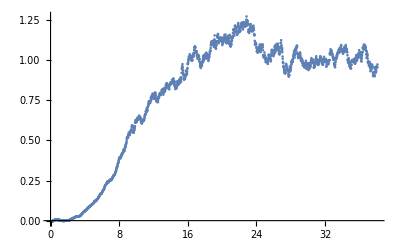

```mathematica
ListPlot[Table[{TimeList⟦i⟧,GammaExList⟦i⟧},{i,lenNum}],PlotRange->All]
```

```mathematica
PolarExList=Import[currentLocation<>goto<>"PolarEx.csv","TSV"];
GammaExErrorList=Flatten[Import[currentLocation<>goto<>"Gamma2Error.csv","TSV"]];
PTimeEx=Import[currentLocation<>goto<>"PTimeEx.csv","TSV"];
GammaTimeEx=Import[currentLocation<>goto<>"GammaTimeEx.csv","TSV"];
```

```mathematica
GammaPeak=Max[GammaExList]+0.05;
Show[
ListPlot[Table[{qq+TimeList⟦i⟧,GammaNumList⟦i,2⟧},{i,1,lenNum,1}],PlotRange->{0,GammaPeak},PlotStyle->Gray],
ListPlot[Table[{qq+TimeList⟦i⟧,GammaNumList⟦i,1⟧},{i,1,lenNum,1}],PlotRange->All,PlotStyle->Red],
ListPlot[Table[{qq+TimeList⟦i⟧,GammaNumList⟦i,3⟧},{i,1,lenNum,1}],PlotRange->All,PlotStyle->Gray],
ListPlot[Table[{TimeList⟦i⟧,GammaExList⟦i⟧},{i,TimeSize}],PlotRange->All,PlotStyle->Blue],

Plot[1-Exp[-(t-qq)/τ]/.τ->GammaTimeEx,{t,0,TimeList⟦-1⟧},PlotStyle->Green],
Plot[1-Exp[-(t-qq)/τ]/.nlmGammaNum["BestFitParameters"],{t,0,TimeList⟦-1⟧},PlotStyle->{Black,Dashed}],
ListPlot[Table[{TimeList⟦i⟧,Around[GammaExList⟦i⟧,GammaExErrorList⟦i⟧]},{i,1,TimeSize,200}],PlotRange->All,PlotStyle->Orange]
]
```

Part::partw: Part 750 of {{-2.03727×10^-13,-2.03727×10^-13,-2.03727×10^-13},{0.00259495,0.00305976,0.00213013},{0.00518443,0.00611311,0.00425577},{0.00776699,0.0091583,0.00637564},{0.0103438,«21»,«21»},«1»,{«1»},{0.018036,0.0212683,0.0148044},{0.0205876,0.0242776,0.0168984},{0.0231329,0.0272799,0.0189873},«739»} does not exist.

Part::partw: Part 751 of {{-2.03727×10^-13,-2.03727×10^-13,-2.03727×10^-13},{0.00259495,0.00305976,0.00213013},{0.00518443,0.00611311,0.00425577},{0.00776699,0.0091583,0.00637564},{0.0103438,«21»,«21»},«1»,{«1»},{0.018036,0.0212683,0.0148044},{0.0205876,0.0242776,0.0168984},{0.0231329,0.0272799,0.0189873},«739»} does not exist.

Part::partw: Part 752 of {{-2.03727×10^-13,-2.03727×10^-13,-2.03727×10^-13},{0.00259495,0.00305976,0.00213013},{0.00518443,0.00611311,0.00425577},{0.00776699,0.0091583,0.00637564},{0.0103438,«21»,«21»},«1»,{«1»},{0.018036,0.0212683,0.0148044},{0.0205876,0.0242776,0.0168984},{0.0231329,0.0272799,0.0189873},«739»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

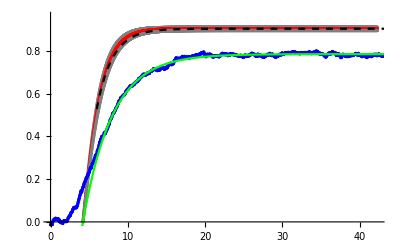

```mathematica
PolarPeak=Max[PolarNumList]+0.05;
Show[
ListPlot[Table[{qp+TimeList⟦i⟧,PolarNumList⟦i,2⟧},{i,1,lenNum,1}],PlotRange->{0,PolarPeak},PlotStyle->Gray],
ListPlot[Table[{qp+TimeList⟦i⟧,PolarNumList⟦i,1⟧},{i,1,lenNum,1}],PlotRange->All,PlotStyle->Red],
ListPlot[Table[{qp+TimeList⟦i⟧,PolarNumList⟦i,3⟧},{i,1,lenNum,1}],PlotRange->All,PlotStyle->Gray],
ListPlot[Table[{TimeList⟦i⟧,PolarExList⟦i⟧},{i,TimeSize}],PlotRange->All,PlotStyle->Blue],
Plot[A(1-Exp[-(t-qp)/τ])/.nlmPTimeEx["BestFitParameters"],{t,0,TimeList⟦-1⟧},PlotStyle->Green,PlotRange->All],
Plot[PolarSteady[γ](1-Exp[-(t-qp)/τ])/.nlmPolarNum["BestFitParameters"],{t,0,TimeList⟦-1⟧},PlotStyle->{Black,Dashed}]
]
```

```mathematica
PSteadyEx=Import[currentLocation<>goto<>"PSteadyEx.csv","TSV"]⟦1,1⟧;
PolarPeak=Max[PolarNumList]+0.05;
Show[
ListPlot[Table[{qp+TimeList⟦i⟧,PolarNumList⟦i,2⟧},{i,1,lenNum,1}],PlotRange->{0,PolarPeak},PlotStyle->Gray],
ListPlot[Table[{qp+TimeList⟦i⟧,PolarNumList⟦i,1⟧},{i,1,lenNum,1}],PlotRange->All,PlotStyle->Red],
ListPlot[Table[{qp+TimeList⟦i⟧,PolarNumList⟦i,3⟧},{i,1,lenNum,1}],PlotRange->All,PlotStyle->Gray],
ListPlot[Table[{TimeList⟦i⟧,PolarExList⟦i⟧},{i,TimeSize}],PlotRange->All,PlotStyle->Blue],
Plot[PSteadyEx(1-Exp[-(t-qp)/τ])/.τ->PTimeEx,{t,0,TimeList⟦-1⟧},PlotStyle->Green,PlotRange->All],
Plot[PolarSteady[γ](1-Exp[-(t-qp)/τ])/.nlmPolarNum["BestFitParameters"],{t,0,TimeList⟦-1⟧},PlotStyle->{Black,Dashed}]
]
```

-Graphics-

```mathematica
Export[currentLocation<>goto<>"PSteadyEx.csv",A/.nlmPTimeEx["BestFitParameters"]];
```

```mathematica
Import[currentLocation<>goto<>"PSteadyEx.csv","TSV"]⟦1,1⟧
```

0.784707

```mathematica
A/.nlmPTimeEx["BestFitParameters"]
```

0.784707